```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
solverRewrite={"SOLVER",{"GPAT"->"A","GP"->"G","NEAT"->"N"}};
distanceRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};

problemRewrite={"gp.demo.SymbolicRegression"->"1D","gp.demo.SymbolicRegression2D"->"2D","gp.demo.SymbolicRegression3D"->"3D","gp.demo.SymbolicRegression4D"->"4D","gp.demo.Maze"->"M1","gp.demo.MazeRangeFinders"->"M2"};
solverLabelRewrite={"SOLVER",{"GPAT"->"AT","GP"->"G","NEAT"->"N"}};
distanceLabelRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
distanceGeneralKLabelRewrite={"GP.DISTANCE_GENERAL_K",{}};
distanceGeneralAlphaLabelRewrite={"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"true"->"1","false"->"0"}};
distanceGeneralBetaLabelRewrite={"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"true"->"1","false"->"0"}};
distanceGPATRewrite={"GPAT.DISTANCE",{"GENERAL"->"G","BASIC"->"I","RANDOM"->"R","Null"->""}};
functionImplRewrite={"gpat.ATFunctions$"->"OR","gpat.ATFunctionsNoConsts$"->"FA","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L","gpat.ATFunctionsComplexifyOnly$"->"CO","gpat.ATFunctionsAllConsts$"->"AC"};
functionImplLabelRewrite={"GPAT.FUNCTION_IMPL",functionImplRewrite};
variantRewrite={"VARIANT",{"BEST"->"B","CHOICE"->"C","Null"->""}};

plotRange={All,{0,100}};
listOfDirectProblems=Grid[{{#[[1]]},{Style[TraditionalForm[#[[2]]],FontSize->12]}}]&/@{{"1D-F",1.5 Subscript[x, 1]^3+2.3 Subscript[x, 1]^2-1.1 Subscript[x, 1]+3.7},{"1D-H",0.1 Subscript[x, 1]^2+0.2Sin[Subscript[x, 1]]},{"2D-I",1.5 Subscript[x, 1] Subscript[x, 2]^2+2.3 Subscript[x, 1] Subscript[x, 2]-1.1 Subscript[x, 2]^2},{"2D-K",Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2},{"3D-E",1.5 Subscript[x, 1] Subscript[x, 2]+2.3 Subscript[x, 1]+Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 3]},{"3D-H",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]+2.3 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 2]+5.3},{"3D-K",Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2] Subscript[x, 3]},{"4D-C",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 4]},{"4D-F",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]-1.1 Subscript[x, 4]},{"4D-G",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3] Subscript[x, 4]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]},{"4D-V",Exp[-1.36709 Subscript[x, 2]^2] Subscript[x, 1](2.43454 Exp[-Subscript[x, 3]^2] -0.393788 Sin[1-Subscript[x, 1]])},{"MAZE-1",""},{"MAZE-2",""}};
listOfDirectProblems={"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"};
listOfIndirectProblems={"Bit Reverse","Bit Shift","Bit Rotate","Parity","Visual Discrimination","Mobile Robot Navigation"};
listOfIndirectProblemsShort={"Bit Reverse","Bit Shift","Bit Rotate","Parity","Visual Discrimination","Robot"};
```

```mathematica
a=27;
b=68.5;
all=200;
testFisherExact[{{0.01a all,all-0.01a all},{0.01b all,all-0.01b all}}]
```

8.05207×10^-17

## Experiments Direct

```mathematica
names={"GP","NEAT_GECCO","AT_G_OR","AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
epilog2={Text[Style[Grid[{{"Algorithm"},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{-1.0,-26}]};
changingParameters[data]
padding={{15,0},{80,25}};
padding2={{40,0},{80,25}};
sortedData = sortDataByParams[data,{"PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE",
"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","SOLVER"}];
sortedData = sortDataByParams[data,{"PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE",
"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","SOLVER"}];
newLabels=extractParameters[sortedData,{
{"SOLVER",{}},
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

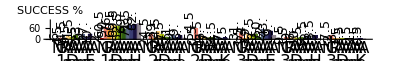

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D","3D"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_1d_2d_3d.eps",%];
```

```mathematica
saveData[selectedData,"DIRECT1"];
```

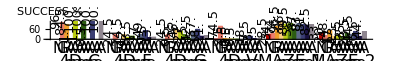

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"4D","M1","M2"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[8;;-1]],2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_4d_maze.eps",%];
```

```mathematica
saveData[selectedData,"DIRECT2"];
```

### Parts

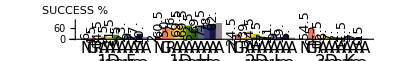

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange,Epilog->{Text[Style[Grid[{{"Algorithm"},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{-1.4,-26}]}, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_1.eps",%];
```

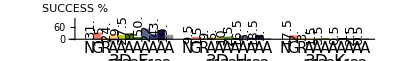

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"3D"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[5;;-1]],2.0,parts,PlotRange->plotRange,Epilog->epilog2, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_2.eps",%];
```

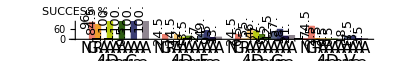

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"4D"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[8;;-1]],2.0,parts,PlotRange->plotRange,Epilog->{Text[Style[Grid[{{"Algorithm"},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{-1.4,-26}]}, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_3.eps",%];
```

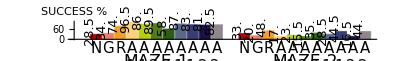

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"M1","M2"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[12;;-1]],2.0,parts,PlotRange->plotRange,Epilog->{Text[Style[Grid[{{"Algorithm"},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{-0.6,-26}]}, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_4.eps",%];
```

## Experiments Indirect

```mathematica
names={"HGP","HNEAT_GECCO","HAT_G_OR","HAT_R","HGP_robo_GP_GECCO","HNEAT_robo_NEAT_GECCO","HAT_G_ROBO","HAT_R_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
epilog2={Text[Style[Grid[{{"Algorithm"},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{-1.0,-26}]};
changingParameters[data]
padding={{15,0},{80,25}};
padding2={{40,0},{80,25}};
sortedData = sortDataByParams[data,{"PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
sortedData = sortDataByParams[data,{"PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT" ,"GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"}];
newLabels=extractParameters[sortedData,{
{"SOLVER",{}},
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",x:__}->{"A",x}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MAX_GENERATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.MUTATION_SUBTREE_PROBABLITY,GP.TARGET_FITNESS,GP.TYPE,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finished,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.generation,PRINT.progress,PRINT.progressShowHyperNet,PRINT.progressShowProblem,PRINT.storeRun,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,SOLVER}

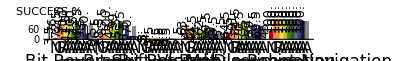

```mathematica
parts = 11;
selectedData=removeData[sortedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{11,1,2,3,4,5,6,7,8,9,10}]&/@Partition[selectedData,parts],1];
selectedData = Flatten[Permute[Partition[selectedData,parts],{2,4,3,6,1,5}],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_indirect.eps",%];
```

```mathematica
saveData[selectedData,"INDIRECT"];
```

### Parts

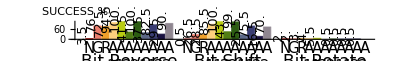

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"RECO"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{11,1,2,3,4,5,6,7,8,9,10}]&/@Partition[selectedData,parts],1];
selectedData = Flatten[Permute[Partition[selectedData,parts],{1,3,2}],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange,Epilog->epilog2, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_5.eps",%];
```

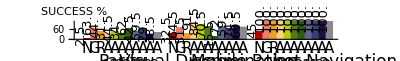

```mathematica
parts = 11;
selectedData=removeData[sortedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"},"PROBLEM"->{"RECO"}}];
selectedData = Flatten[Permute[#,{11,1,2,3,4,5,6,7,8,9,10}]&/@Partition[selectedData,parts],1];
selectedData = Flatten[Permute[Partition[selectedData,parts],{3,1,2}],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems[[4;;-1]],2.0,parts,PlotRange->plotRange,Epilog->epilog2, ImagePadding->padding2,AspectRatio->0.25/GoldenRatio,ImageSize->{{800},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_6.eps",%];
```

## Experiments Direct PRESENTATION

```mathematica
names={"T/NEAT","T/GP","T/AT_G_OR_BEST","T/AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
sortedData=removeData[sortedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}]; (* Removed 2D-J *)
sortedData=removeData[sortedData,{"GPAT.FUNCTION_IMPL"->{"gpat.ATFunctionsNoConsts$","gpat.ATFunctionsLikeGP$","gpat.ATFunctionsComplexifyOnly$","gpat.ATFunctionsAllConsts$"}}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite,
distanceGPATRewrite,
variantRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G","","",""}->{"T","",""},{"G",x:__}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T","",""}->{"G",""}}];
newLabels=ReplaceAll[newLabels,{{"N","","",""}->{"N",""}}];
newLabels=ReplaceAll[newLabels,{{"E",x:_,"",y:_}->{"E",Subscript[x,y]}}];
newLabels=ReplaceAll[newLabels,{{"E",x:_,""}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"A","",x:_,y:_}->{"A",x}}];
(*newLabels=ReplaceAll[newLabels,{{"E",x:_,""}->{"E",x}}];*)
sortedData=replaceLabels[sortedData,newLabels];
parts=4;
sortedData = Flatten[Permute[#,{4,1,3,2}]&/@Partition[sortedData,parts],1];
printAsTable[sortedData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","VARIANT","GPAT.FUNCTION_IMPL"}]
```

ID | PARAM FILE | SOLVER | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GP.DISTANCE | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | VARIANT | GPAT.FUNCTION_IMPL
{N,} | T/NEAT/parameters_001.txt | NEAT | 1D | F |  |  |  |  | gp.demo.SymbolicRegression |  | 
{G,} | T/GP/parameters_001.txt | GP | 1D | F |  |  |  |  | gp.demo.SymbolicRegression |  | 
{A,R} | T/AT_R/parameters_001.txt | GPAT | 1D | F |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_001.txt | GPAT | 1D | F |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_002.txt | NEAT | 1D | H |  |  |  |  | gp.demo.SymbolicRegression |  | 
{G,} | T/GP/parameters_002.txt | GP | 1D | H |  |  |  |  | gp.demo.SymbolicRegression |  | 
{A,R} | T/AT_R/parameters_004.txt | GPAT | 1D | H |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_002.txt | GPAT | 1D | H |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_003.txt | NEAT | 2D | I |  |  |  |  | gp.demo.SymbolicRegression2D |  | 
{G,} | T/GP/parameters_003.txt | GP | 2D | I |  |  |  |  | gp.demo.SymbolicRegression2D |  | 
{A,R} | T/AT_R/parameters_007.txt | GPAT | 2D | I |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression2D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_003.txt | GPAT | 2D | I |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression2D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_004.txt | NEAT | 2D | K |  |  |  |  | gp.demo.SymbolicRegression2D |  | 
{G,} | T/GP/parameters_005.txt | GP | 2D | K |  |  |  |  | gp.demo.SymbolicRegression2D |  | 
{A,R} | T/AT_R/parameters_010.txt | GPAT | 2D | K |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression2D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_004.txt | GPAT | 2D | K |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression2D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_005.txt | NEAT | 3D | E |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{G,} | T/GP/parameters_006.txt | GP | 3D | E |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{A,R} | T/AT_R/parameters_013.txt | GPAT | 3D | E |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_005.txt | GPAT | 3D | E |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_006.txt | NEAT | 3D | H |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{G,} | T/GP/parameters_007.txt | GP | 3D | H |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{A,R} | T/AT_R/parameters_016.txt | GPAT | 3D | H |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_006.txt | GPAT | 3D | H |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_007.txt | NEAT | 3D | K |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{G,} | T/GP/parameters_008.txt | GP | 3D | K |  |  |  |  | gp.demo.SymbolicRegression3D |  | 
{A,R} | T/AT_R/parameters_019.txt | GPAT | 3D | K |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_007.txt | GPAT | 3D | K |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression3D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_008.txt | NEAT | 4D | C |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{G,} | T/GP/parameters_009.txt | GP | 4D | C |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{A,R} | T/AT_R/parameters_022.txt | GPAT | 4D | C |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_008.txt | GPAT | 4D | C |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_009.txt | NEAT | 4D | F |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{G,} | T/GP/parameters_010.txt | GP | 4D | F |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{A,R} | T/AT_R/parameters_025.txt | GPAT | 4D | F |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_009.txt | GPAT | 4D | F |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_010.txt | NEAT | 4D | G |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{G,} | T/GP/parameters_011.txt | GP | 4D | G |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{A,R} | T/AT_R/parameters_028.txt | GPAT | 4D | G |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_010.txt | GPAT | 4D | G |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_011.txt | NEAT | 4D | ZFC55 |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{G,} | T/GP/parameters_012.txt | GP | 4D | ZFC55 |  |  |  |  | gp.demo.SymbolicRegression4D |  | 
{A,R} | T/AT_R/parameters_031.txt | GPAT | 4D | ZFC55 |  |  | RANDOM | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_011.txt | GPAT | 4D | ZFC55 |  |  | GENERAL | gpat.ATFunctions$ | gp.demo.SymbolicRegression4D | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_012.txt | NEAT | MAZE |  | map2.csv |  |  |  | gp.demo.Maze |  | 
{G,} | T/GP/parameters_013.txt | GP | MAZE |  | map2.csv |  |  |  | gp.demo.Maze |  | 
{A,R} | T/AT_R/parameters_034.txt | GPAT | MAZE |  | map2.csv |  | RANDOM | gpat.ATFunctions$ | gp.demo.Maze |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_012.txt | GPAT | MAZE |  | map2.csv |  | GENERAL | gpat.ATFunctions$ | gp.demo.Maze | BEST | gpat.ATFunctions$
{N,} | T/NEAT/parameters_013.txt | NEAT | MAZE |  | map4.csv |  |  |  | gp.demo.MazeRangeFinders |  | 
{G,} | T/GP/parameters_014.txt | GP | MAZE |  | map4.csv |  |  |  | gp.demo.MazeRangeFinders |  | 
{A,R} | T/AT_R/parameters_037.txt | GPAT | MAZE |  | map4.csv |  | RANDOM | gpat.ATFunctions$ | gp.demo.MazeRangeFinders |  | gpat.ATFunctions$
{A,G} | T/AT_G_OR_BEST/parameters_013.txt | GPAT | MAZE |  | map4.csv |  | GENERAL | gpat.ATFunctions$ | gp.demo.MazeRangeFinders | BEST | gpat.ATFunctions$

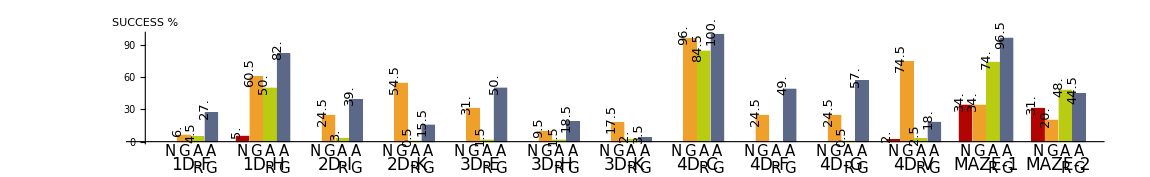

```mathematica
selectedData=selectData[sortedData,{"ID"->{"1D","2D","3D","4D","MAZE"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-1.3,-10.5}]};
padding={{40,0},{60,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,0.0,parts,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding,BarLabelsRotate->Pi/2,ImageSize->1150,AspectRatio->0.25/GoldenRatio,Colors->listOfColors[10][[{1,3,5,8}]]]
Export["gpat_soco_all_direct.pdf",%];
```

## Experiments Indirect PRESENTATIONS

```mathematica
names={"T/HNEAT","T/HGP","T/HAT_G_OR_BEST","T/HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.0,-10.5}]};
padding={{30,0},{60,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
sortedData=removeData[sortedData,{"GPAT.FUNCTION_IMPL"->{"gpat.ATFunctionsNoConsts$","gpat.ATFunctionsLikeGP$","gpat.ATFunctionsComplexifyOnly$","gpat.ATFunctionsAllConsts$"}}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite,
distanceGPATRewrite,
variantRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G","","",""}->{"T","",""},{"G",x:__}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T","",""}->{"G",""}}];
newLabels=ReplaceAll[newLabels,{{"N","","",""}->{"N",""}}];
newLabels=ReplaceAll[newLabels,{{"E",x:_,"",y:_}->{"E",Subscript[x,y]}}];
newLabels=ReplaceAll[newLabels,{{"E",x:_,""}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"A","",x:_,y:_}->{"A",x}}];
(*newLabels=ReplaceAll[newLabels,{{"E",x:_,""}->{"E",x}}];*)
sortedData=replaceLabels[sortedData,newLabels];
parts=4;
sortedData = Flatten[Permute[#,{4,1,3,2}]&/@Partition[sortedData,parts],1];
printAsTable[sortedData,{"SOLVER","GP.TYPE","ID","GP.DISTANCE","GPAT.DISTANCE","RECO.GENERATOR","PROBLEM","VARIANT","GPAT.FUNCTION_IMPL"}]
```

ID | PARAM FILE | SOLVER | GP.TYPE | ID | GP.DISTANCE | GPAT.DISTANCE | RECO.GENERATOR | PROBLEM | VARIANT | GPAT.FUNCTION_IMPL
{N,} | T/HNEAT/parameters_004.txt | NEAT |  | FC |  |  |  | FIND_CLUSTER |  | 
{G,} | T/HGP/parameters_001.txt | GP | gp.GP | FC |  |  |  | FIND_CLUSTER |  | 
{A,R} | T/HAT_R/parameters_010.txt | GPAT | gpat.GPAT | FC |  | RANDOM |  | FIND_CLUSTER |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_001.txt | GPAT | gpat.GPAT | FC |  | GENERAL |  | FIND_CLUSTER | BEST | gpat.ATFunctions$
{N,} | T/HNEAT/parameters_001.txt | NEAT |  | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO |  | 
{G,} | T/HGP/parameters_002.txt | GP | gp.GP | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO |  | 
{A,R} | T/HAT_R/parameters_001.txt | GPAT | gpat.GPAT | RECO1D |  | RANDOM | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_002.txt | GPAT | gpat.GPAT | RECO1D |  | GENERAL | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO | BEST | gpat.ATFunctions$
{N,} | T/HNEAT/parameters_003.txt | NEAT |  | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO |  | 
{G,} | T/HGP/parameters_004.txt | GP | gp.GP | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO |  | 
{A,R} | T/HAT_R/parameters_007.txt | GPAT | gpat.GPAT | RECO1D |  | RANDOM | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_003.txt | GPAT | gpat.GPAT | RECO1D |  | GENERAL | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO | BEST | gpat.ATFunctions$
{N,} | T/HNEAT/parameters_002.txt | NEAT |  | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO |  | 
{G,} | T/HGP/parameters_003.txt | GP | gp.GP | RECO1D |  |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO |  | 
{A,R} | T/HAT_R/parameters_004.txt | GPAT | gpat.GPAT | RECO1D |  | RANDOM | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_004.txt | GPAT | gpat.GPAT | RECO1D |  | GENERAL | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO | BEST | gpat.ATFunctions$
{N,} | T/HNEAT/parameters_006.txt | NEAT |  | ROBO |  |  |  | ROBOTS |  | 
{G,} | T/HGP/parameters_006.txt | GP | gp.GP | ROBO |  |  |  | ROBOTS |  | 
{A,R} | T/HAT_R/parameters_016.txt | GPAT | gpat.GPAT | ROBO |  | RANDOM |  | ROBOTS |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_006.txt | GPAT | gpat.GPAT | ROBO |  | GENERAL |  | ROBOTS | BEST | gpat.ATFunctions$
{N,} | T/HNEAT/parameters_005.txt | NEAT |  | XOR |  |  | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR |  | 
{G,} | T/HGP/parameters_005.txt | GP | gp.GP | XOR |  |  | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR |  | 
{A,R} | T/HAT_R/parameters_013.txt | GPAT | gpat.GPAT | XOR |  | RANDOM | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR |  | gpat.ATFunctions$
{A,G} | T/HAT_G_OR_BEST/parameters_005.txt | GPAT | gpat.GPAT | XOR |  | GENERAL | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR | BEST | gpat.ATFunctions$

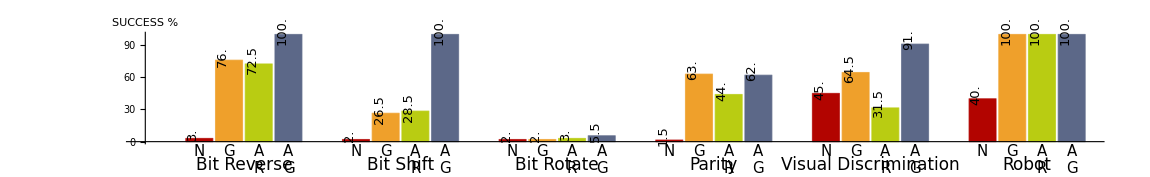

```mathematica
selectedData=sortedData;
selectedData = Flatten[Permute[Partition[selectedData,parts],{2,4,3,6,1,5}],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblemsShort,0.0,parts,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding,BarLabelsRotate->Pi/2,ImageSize->1150,AspectRatio->0.25/GoldenRatio,Colors->listOfColors[10][[{1,3,5,8}]]]
Export["gpat_all_indirect.pdf",%];
```